```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Caden Gobat\Documents\GitHub\PHYS-3181\homework10

```mathematica
p2data=ReadList["p2.log",{Number,Number,Number}]
```

{{-14.697,-14.697,300.282},{-14.3939,-14.697,300.564},{-14.0909,-14.697,300.846},6162,{14.0909,14.697,300.846},{14.3939,14.697,300.564},{14.697,14.697,300.282}}
 |  |  |  |

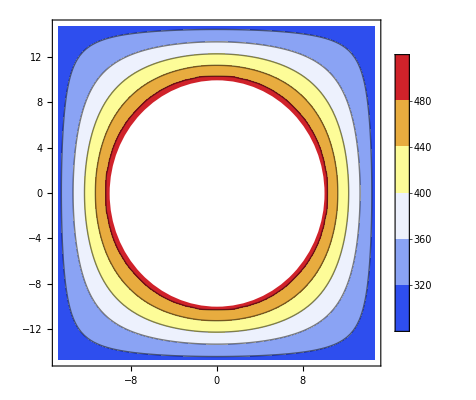

```mathematica
Show[ListContourPlot[p2data,Contours->{320,360,400,440,480},ColorFunction->"TemperatureMap",PlotLegends->Automatic],Graphics[{White,Disk[{0,0},10]}]]
```

```mathematica
p2gradient=ReadList["p2grad.log",{{Number,Number},{Number,Number}}]
```

{{{-14.697,-14.697},{0.930552,0.930552}},{{-14.3939,-14.697},{0.930551,1.86111}},6164,{{14.3939,14.697},{-0.930551,-1.86111}},{{14.697,14.697},{-0.930552,-0.930552}}}
 |  |  |  |

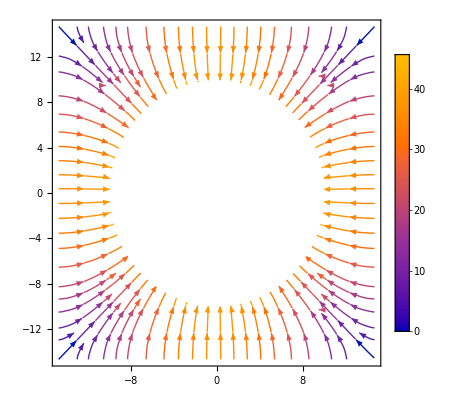

```mathematica
Show[ListStreamPlot[p2gradient,PlotLegends->Automatic],Graphics[{White,Disk[{0,0},10]}]]
```

```mathematica
iters={{61,6854},{73,5714},{85,4906},{97,4286},{109,3792},{121,3398},{133,3068},{145,2783},{157,2544},{169,},{181,},{193,},{205,},{217,},{229,},{241,},
```